## Puntos del lobo

```mathematica
lobo = {{3.102, 4.304}, {2.94, 4.152}, {2.88, 4.452}, {2.866, 4.896}, {2.776, 4.496}, {2.584, 3.952}, {2.496, 3.636}, {2.236, 3.072}, {2.052, 2.62}, {1.836, 2.2}, {1.606, 1.792}, {1.34, 1.428}, {1.006, 1.}, {1.496, 1.012}, {1.784, 1.548}, {2.096, 2.192}, {2.288, 2.612}, {2.51, 3.148}, {2.658, 3.56}, {2.814, 3.976}, {2.97, 3.672}, {3.228, 3.304}, {3.518, 2.968}, {3.902, 2.56}, {4.436, 2.064}, {3.392, 2.072}, {2.814, 2.116}, {2.406, 2.2}, {2.228, 1.904}, {2.754, 1.888}, {2.644, 1.584}, {2.592, 1.304}, {2.614, 1.004}, {3.08, 1.}, {2.932, 1.168}, {2.828, 1.352}, {2.858, 1.584}, {2.97, 1.888}, {3.57, 1.888}, {4.014, 1.888}, {4.926, 1.896}, {4.11, 2.636}, {3.326, 3.464}, {3.37, 3.896}, {3.444, 4.124}, {3.658, 4.696}, {3.466, 4.584}, {3.414, 4.332}, {3.236, 3.904}, {3.176, 3.656}, {3.014, 3.916}, {3.11, 4.104}, {3.42, 4.38}, {3.462, 4.58}, {3.102, 4.304}};
ojo = {{3.332, 2.644}, {3.6, 2.604}, {3.436, 2.776}, {3.266, 2.896}, {3.044, 2.992}, {2.902, 2.984}, {2.822, 2.88}, {2.888, 2.724}, {3.162, 2.68}};
```

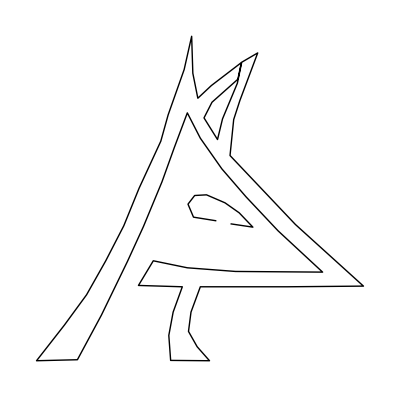

```mathematica
Graphics[Line[{lobo, ojo}]]
```

```mathematica
c1 = Flatten[Table[Transpose[({{0.5, 0}, {0, 0.5}}).({{lobo[[i,1]]}, {lobo[[i,2]]}})],{i,Length[lobo]}],1];
```

```mathematica
ojo1 = Flatten[Table[Transpose[({{0.5, 0}, {0, 0.5}}).({{ojo[[i,1]]}, {ojo[[i,2]]}})],{i,Length[ojo]}],1]
```

{{1.666,1.322},{1.8,1.302},{1.718,1.388},{1.633,1.448},{1.522,1.496},{1.451,1.492},{1.411,1.44},{1.444,1.362},{1.581,1.34}}

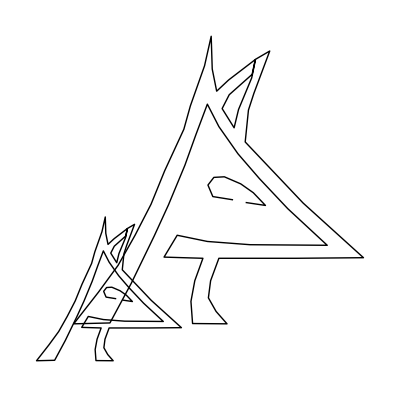

```mathematica
Graphics[Line[{lobo,c1, ojo,ojo1}]]
```

```mathematica
Manipulate[
Graphics[
Line[
{lobo,Flatten[Table[Transpose[({{k, 0}, {0, k}}).({{lobo[[i,1]]}, {lobo[[i,2]]}})],{i,1,Length[lobo]}],1],ojo,Flatten[Table[Transpose[({{k, 0}, {0, k}}).({{ojo[[i,1]]}, {ojo[[i,2]]}})],{i,Length[ojo]}],1]}],PlotRange->{{-5,10},{0,10}}],{k,0,2}]
```

```mathematica
Manipulate[
Graphics[
Line[
{lobo,Flatten[Table[Transpose[({{Cos[k], Sin[k]}, {-Sin[k], Cos[k]}}).({{lobo[[i,1]]}, {lobo[[i,2]]}})],{i,1,Length[lobo]}],1]}],PlotRange->{{-10,10},{-10,10}}],{k,0,4 Pi}]
```